```mathematica
β[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=
β[ω,δ,t,ϵ1,ϵ2,m]=ReplacePart[ReplacePart[ReplacePart[0*IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->t],Table[{a,a},{a,1,2m,2}]->ω+ⅈ*δ-ϵ1],Table[{b,b},{b,2,2m,2}]->ω+ⅈ*δ-ϵ2]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
leads= Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/hBN/leads/lead_right_1_0.75_hbn_"<>ToString[ω]<>".dat"]],{ω,Range[-3.5,3.5,0.01]}]
```

{1}
 |  |  |  |

```mathematica
Clear[LEFT,SR]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=LEFT[ω,δ,t,ϵ1,ϵ2,m]=(*leads[[Round[ω*100+351]]]*)Module[{J=Inverse[β[ω,δ,t,ϵ1,ϵ2,m]],B:=Inverse[β[ω,δ,t,ϵ1,ϵ2,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,10000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= Inverse[β[ω,δ,t,ϵ1,ϵ2,m]]
SR[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ1,ϵ2,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ1,ϵ2,m].T1[t,m]].g[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=SR[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m].SR[ω,δ,t,ϵ2,ϵ1,m].ConjugateTranspose[ρ[t,m]]].SL[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ2,ϵ1,m].ρ[t,m].SL[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m]].SR[ω,δ,t,ϵ2,ϵ1,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= IL[ω,δ,t,ϵ1,ϵ2,m]-ConjugateTranspose[IL[ω,δ,t,ϵ1,ϵ2,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= IR[ω,δ,t,ϵ1,ϵ2,m]-ConjugateTranspose[IR[ω,δ,t,ϵ1,ϵ2,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= SR[ω,δ,t,ϵ2,ϵ1,m].ρ[t,m].IL[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= Gnonlocal[ω,δ,t,ϵ1,ϵ2,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ1,ϵ2,m]]
```

```mathematica
pris[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m].grr[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m].GNON[ω,δ,t,ϵ1,ϵ2,m]]]
```

```mathematica
Table[{ω,Print[ω];pris[ω,0.0001,1,0,0,9]},{ω,Range[-3,3,0.01]}]
```

0.26

0.27

0.28

0.29

0.3

0.31

0.32

0.33

0.34

0.35

0.36

0.37

0.38

0.39

0.4

0.41

0.42

0.43

0.44

0.45

0.46

0.47

0.48

0.49

0.5

0.51

0.52

0.53

0.54

0.55

0.56

0.57

0.58

0.59

0.6

0.61

0.62

0.63

0.64

0.65

0.66

0.67

0.68

0.69

0.7

0.71

0.72

0.73

0.74

0.75

0.76

0.77

0.78

0.79

0.8

0.81

0.82

0.83

0.84

0.85

0.86

0.87

0.88

0.89

0.9

0.91

0.92

0.93

0.94

0.95

0.96

0.97

0.98

0.99

1.

1.01

1.02

1.03

1.04

1.05

1.06

1.07

1.08

1.09

1.1

1.11

1.12

1.13

1.14

1.15

1.16

1.17

1.18

1.19

1.2

1.21

1.22

1.23

1.24

1.25

1.26

1.27

1.28

1.29

1.3

1.31

1.32

1.33

1.34

1.35

1.36

1.37

1.38

1.39

1.4

1.41

1.42

1.43

1.44

1.45

1.46

1.47

1.48

1.49

1.5

1.51

1.52

1.53

1.54

1.55

1.56

1.57

1.58

1.59

1.6

1.61

1.62

1.63

1.64

1.65

1.66

1.67

1.68

1.69

1.7

1.71

1.72

1.73

1.74

1.75

1.76

1.77

1.78

1.79

1.8

1.81

1.82

1.83

1.84

1.85

1.86

1.87

1.88

1.89

1.9

1.91

1.92

1.93

1.94

1.95

1.96

1.97

1.98

1.99

2.

2.01

2.02

2.03

2.04

2.05

2.06

2.07

2.08

2.09

2.1

2.11

2.12

2.13

2.14

2.15

2.16

2.17

2.18

2.19

2.2

2.21

2.22

2.23

2.24

2.25

2.26

2.27

2.28

2.29

2.3

2.31

2.32

2.33

2.34

2.35

2.36

2.37

2.38

2.39

2.4

2.41

2.42

2.43

2.44

2.45

2.46

2.47

2.48

2.49

2.5

2.51

2.52

2.53

2.54

2.55

2.56

2.57

2.58

2.59

2.6

2.61

2.62

2.63

2.64

2.65

2.66

2.67

2.68

2.69

2.7

2.71

2.72

2.73

2.74

2.75

2.76

2.77

2.78

2.79

2.8

2.81

2.82

2.83

2.84

2.85

2.86

2.87

2.88

2.89

2.9

2.91

2.92

2.93

2.94

2.95

2.96

2.97

2.98

2.99

3.

{{-3.,2.57847×10^-7},{-2.99,3.1912×10^-7},{-2.98,4.0555×10^-7},{-2.97,5.33087×10^-7},{-2.96,7.32637×10^-7},{-2.95,1.07063×10^-6},{-2.94,1.71217×10^-6},{-2.93,3.16731×10^-6},{-2.92,7.72697×10^-6},{-2.91,0.0000399553},{-2.9,0.99944},{-2.89,0.999983},{-2.88,0.999995},{-2.87,0.999998},{-2.86,0.999999},{-2.85,0.999999},{-2.84,0.999999},{-2.83,1.},{-2.82,1.},{-2.81,1.},{-2.8,1.},{-2.79,1.},{-2.78,1.},{-2.77,1.},{-2.76,1.},{-2.75,1.},{-2.74,1.},{-2.73,1.},{-2.72,1.},{-2.71,1.},{-2.7,1.},{-2.69,1.},{-2.68,1.},{-2.67,1.},{-2.66,1.},{-2.65,1.},{-2.64,1.},{-2.63,1.00002},{-2.62,1.00064},{-2.61,1.99996},{-2.6,1.99999},{-2.59,2.},{-2.58,2.},{-2.57,2.},{-2.56,1.99998},{-2.55,1.99999},{-2.54,1.99998},{-2.53,1.99998},{-2.52,1.99999},{-2.51,1.99997},{-2.5,2.},{-2.49,1.99998},{-2.48,1.99996},{-2.47,2.},{-2.46,1.99998},{-2.45,1.99996},{-2.44,2.},{-2.43,1.99995},{-2.42,1.99997},{-2.41,1.99991},{-2.4,1.99991},{-2.39,1.99992},{-2.38,1.99994},{-2.37,1.99997},{-2.36,1.99989},{-2.35,1.99993},{-2.34,1.99986},{-2.33,1.99997},{-2.32,1.99999},{-2.31,2.},{-2.3,2.},{-2.29,1.99998},{-2.28,1.99996},{-2.27,1.99995},{-2.26,1.99996},{-2.25,1.99999},{-2.24,1.99981},{-2.23,1.99974},{-2.22,1.99988},{-2.21,1.99998},{-2.2,1.99993},{-2.19,2.},{-2.18,1.9997},{-2.17,2.99981},{-2.16,2.99993},{-2.15,2.99958},{-2.14,2.99998},{-2.13,2.99997},{-2.12,2.99963},{-2.11,2.99992},{-2.1,2.99986},{-2.09,2.99942},{-2.08,2.99942},{-2.07,3.},{-2.06,2.99985},{-2.05,2.99966},{-2.04,3.},{-2.03,2.99933},{-2.02,2.99957},{-2.01,2.99911},{-2.,2.99905},{-1.99,2.99984},{-1.98,2.99979},{-1.97,2.99934},{-1.96,2.99991},{-1.95,2.99975},{-1.94,2.99925},{-1.93,2.99893},{-1.92,2.99959},{-1.91,2.9991},{-1.9,2.99927},{-1.89,2.99898},{-1.88,2.99955},{-1.87,2.99987},{-1.86,2.99995},{-1.85,2.99868},{-1.84,2.99979},{-1.83,2.99969},{-1.82,2.99972},{-1.81,2.99835},{-1.8,2.99933},{-1.79,2.99975},{-1.78,2.99941},{-1.77,2.99951},{-1.76,2.99825},{-1.75,2.99939},{-1.74,2.99917},{-1.73,2.99872},{-1.72,2.99806},{-1.71,2.99812},{-1.7,2.99917},{-1.69,2.99959},{-1.68,2.99866},{-1.67,2.99968},{-1.66,2.99874},{-1.65,2.99962},{-1.64,2.99848},{-1.63,2.99911},{-1.62,3.00001},{-1.61,3.99789},{-1.6,3.99983},{-1.59,3.99882},{-1.58,3.99915},{-1.57,3.99877},{-1.56,3.99826},{-1.55,3.99852},{-1.54,3.99917},{-1.53,3.99969},{-1.52,3.9994},{-1.51,3.99875},{-1.5,3.99946},{-1.49,3.99871},{-1.48,3.99966},{-1.47,3.9989},{-1.46,3.99982},{-1.45,3.99801},{-1.44,3.99838},{-1.43,3.99809},{-1.42,3.99947},{-1.41,3.99801},{-1.4,3.99957},{-1.39,3.99854},{-1.38,3.99896},{-1.37,3.99878},{-1.36,3.99867},{-1.35,3.99911},{-1.34,3.99859},{-1.33,3.99899},{-1.32,3.99909},{-1.31,3.99914},{-1.3,3.99835},{-1.29,3.99973},{-1.28,3.9981},{-1.27,3.99867},{-1.26,3.99912},{-1.25,3.99829},{-1.24,3.99908},{-1.23,3.99878},{-1.22,3.99938},{-1.21,3.9986},{-1.2,3.99962},{-1.19,3.99862},{-1.18,3.99856},{-1.17,3.99826},{-1.16,3.9992},{-1.15,3.99901},{-1.14,3.99862},{-1.13,3.99817},{-1.12,3.99893},{-1.11,3.99848},{-1.1,3.99984},{-1.09,3.99932},{-1.08,3.99958},{-1.07,3.99874},{-1.06,3.99928},{-1.05,3.99905},{-1.04,3.99915},{-1.03,3.99941},{-1.02,3.99845},{-1.01,3.99916},{-1.,4.},{-0.99,3.99922},{-0.98,3.99967},{-0.97,3.99862},{-0.96,3.99965},{-0.95,3.99944},{-0.94,3.99986},{-0.93,3.99952},{-0.92,3.99895},{-0.91,3.99914},{-0.9,2.99931},{-0.89,2.99859},{-0.88,2.99933},{-0.87,2.99912},{-0.86,2.99993},{-0.85,2.99972},{-0.84,2.99973},{-0.83,2.99915},{-0.82,2.99952},{-0.81,2.99879},{-0.8,2.99892},{-0.79,2.99891},{-0.78,2.99876},{-0.77,2.99992},{-0.76,2.99876},{-0.75,2.99983},{-0.74,2.99983},{-0.73,2.99955},{-0.72,2.9996},{-0.71,2.99995},{-0.7,2.99968},{-0.69,2.9987},{-0.68,2.99976},{-0.67,2.99905},{-0.66,2.99966},{-0.65,2.9988},{-0.64,2.99999},{-0.63,2.99885},{-0.62,2.99859},{-0.61,1.99996},{-0.6,1.99871},{-0.59,1.99967},{-0.58,1.9993},{-0.57,1.99929},{-0.56,1.99917},{-0.55,1.99993},{-0.54,1.99904},{-0.53,1.99873},{-0.52,1.99876},{-0.51,1.99929},{-0.5,1.99988},{-0.49,1.99916},{-0.48,1.99881},{-0.47,1.99903},{-0.46,1.99994},{-0.45,1.99977},{-0.44,2.},{-0.43,1.99905},{-0.42,1.99934},{-0.41,1.99925},{-0.4,1.99908},{-0.39,1.99903},{-0.38,1.00048},{-0.37,0.999364},{-0.36,0.999889},{-0.35,0.999445},{-0.34,0.99936},{-0.33,0.999427},{-0.32,0.999672},{-0.31,0.99983},{-0.3,0.999615},{-0.29,0.99963},{-0.28,0.999703},{-0.27,0.999942},{-0.26,0.999878},{-0.25,1.},{-0.24,0.999999},{-0.23,0.999967},{-0.22,0.999979},{-0.21,0.999995},{-0.2,0.999999},{-0.19,0.99999},{-0.18,0.999875},{-0.17,0.0000824994},{-0.16,0.0000111511},{-0.15,4.41743×10^-6},{-0.14,2.46089×10^-6},{-0.13,1.62723×10^-6},{-0.12,1.19349×10^-6},{-0.11,9.38337×10^-7},{-0.1,7.75354×10^-7},{-0.09,6.65062×10^-7},{-0.08,5.8731×10^-7},{-0.07,5.3093×10^-7},{-0.06,4.89339×10^-7},{-0.05,4.58469×10^-7},{-0.04,4.35721×10^-7},{-0.03,4.19402×10^-7},{-0.02,4.08416×10^-7},{-0.01,4.02074×10^-7},{0.,4.×10^-7},{0.01,4.02074×10^-7},{0.02,4.08416×10^-7},{0.03,4.19402×10^-7},{0.04,4.35721×10^-7},{0.05,4.58469×10^-7},{0.06,4.89339×10^-7},{0.07,5.3093×10^-7},{0.08,5.8731×10^-7},{0.09,6.65062×10^-7},{0.1,7.75354×10^-7},{0.11,9.38337×10^-7},{0.12,1.19349×10^-6},{0.13,1.62723×10^-6},{0.14,2.46089×10^-6},{0.15,4.41743×10^-6},{0.16,0.0000111511},{0.17,0.0000824994},{0.18,0.999875},{0.19,0.99999},{0.2,0.999999},{0.21,0.999995},{0.22,0.999979},{0.23,0.999967},{0.24,0.999999},{0.25,1.},{0.26,0.999878},{0.27,0.999942},{0.28,0.999703},{0.29,0.99963},{0.3,0.999615},{0.31,0.99983},{0.32,0.999672},{0.33,0.999427},{0.34,0.99936},{0.35,0.999445},{0.36,0.999889},{0.37,0.999364},{0.38,1.00048},{0.39,1.99903},{0.4,1.99908},{0.41,1.99925},{0.42,1.99934},{0.43,1.99905},{0.44,2.},{0.45,1.99977},{0.46,1.99994},{0.47,1.99903},{0.48,1.99881},{0.49,1.99916},{0.5,1.99988},{0.51,1.99929},{0.52,1.99876},{0.53,1.99873},{0.54,1.99904},{0.55,1.99993},{0.56,1.99917},{0.57,1.99929},{0.58,1.9993},{0.59,1.99967},{0.6,1.99871},{0.61,1.99996},{0.62,2.99859},{0.63,2.99885},{0.64,2.99999},{0.65,2.9988},{0.66,2.99966},{0.67,2.99905},{0.68,2.99976},{0.69,2.9987},{0.7,2.99968},{0.71,2.99995},{0.72,2.9996},{0.73,2.99955},{0.74,2.99983},{0.75,2.99983},{0.76,2.99876},{0.77,2.99992},{0.78,2.99876},{0.79,2.99891},{0.8,2.99892},{0.81,2.99879},{0.82,2.99952},{0.83,2.99915},{0.84,2.99973},{0.85,2.99972},{0.86,2.99993},{0.87,2.99912},{0.88,2.99933},{0.89,2.99859},{0.9,2.99931},{0.91,3.99914},{0.92,3.99895},{0.93,3.99952},{0.94,3.99986},{0.95,3.99944},{0.96,3.99965},{0.97,3.99862},{0.98,3.99967},{0.99,3.99922},{1.,4.},{1.01,3.99916},{1.02,3.99845},{1.03,3.99941},{1.04,3.99915},{1.05,3.99905},{1.06,3.99928},{1.07,3.99874},{1.08,3.99958},{1.09,3.99932},{1.1,3.99984},{1.11,3.99848},{1.12,3.99893},{1.13,3.99817},{1.14,3.99862},{1.15,3.99901},{1.16,3.9992},{1.17,3.99826},{1.18,3.99856},{1.19,3.99862},{1.2,3.99962},{1.21,3.9986},{1.22,3.99938},{1.23,3.99878},{1.24,3.99908},{1.25,3.99829},{1.26,3.99912},{1.27,3.99867},{1.28,3.9981},{1.29,3.99973},{1.3,3.99835},{1.31,3.99914},{1.32,3.99909},{1.33,3.99899},{1.34,3.99859},{1.35,3.99911},{1.36,3.99867},{1.37,3.99878},{1.38,3.99896},{1.39,3.99854},{1.4,3.99957},{1.41,3.99801},{1.42,3.99947},{1.43,3.99809},{1.44,3.99838},{1.45,3.99801},{1.46,3.99982},{1.47,3.9989},{1.48,3.99966},{1.49,3.99871},{1.5,3.99946},{1.51,3.99875},{1.52,3.9994},{1.53,3.99969},{1.54,3.99917},{1.55,3.99852},{1.56,3.99826},{1.57,3.99877},{1.58,3.99915},{1.59,3.99882},{1.6,3.99983},{1.61,3.99789},{1.62,3.00001},{1.63,2.99911},{1.64,2.99848},{1.65,2.99962},{1.66,2.99874},{1.67,2.99968},{1.68,2.99866},{1.69,2.99959},{1.7,2.99917},{1.71,2.99812},{1.72,2.99806},{1.73,2.99872},{1.74,2.99917},{1.75,2.99939},{1.76,2.99825},{1.77,2.99951},{1.78,2.99941},{1.79,2.99975},{1.8,2.99933},{1.81,2.99835},{1.82,2.99972},{1.83,2.99969},{1.84,2.99979},{1.85,2.99868},{1.86,2.99995},{1.87,2.99987},{1.88,2.99955},{1.89,2.99898},{1.9,2.99927},{1.91,2.9991},{1.92,2.99959},{1.93,2.99893},{1.94,2.99925},{1.95,2.99975},{1.96,2.99991},{1.97,2.99934},{1.98,2.99979},{1.99,2.99984},{2.,2.99905},{2.01,2.99911},{2.02,2.99957},{2.03,2.99933},{2.04,3.},{2.05,2.99966},{2.06,2.99985},{2.07,3.},{2.08,2.99942},{2.09,2.99942},{2.1,2.99986},{2.11,2.99992},{2.12,2.99963},{2.13,2.99997},{2.14,2.99998},{2.15,2.99958},{2.16,2.99993},{2.17,2.99981},{2.18,1.9997},{2.19,2.},{2.2,1.99993},{2.21,1.99998},{2.22,1.99988},{2.23,1.99974},{2.24,1.99981},{2.25,1.99999},{2.26,1.99996},{2.27,1.99995},{2.28,1.99996},{2.29,1.99998},{2.3,2.},{2.31,2.},{2.32,1.99999},{2.33,1.99997},{2.34,1.99986},{2.35,1.99993},{2.36,1.99989},{2.37,1.99997},{2.38,1.99994},{2.39,1.99992},{2.4,1.99991},{2.41,1.99991},{2.42,1.99997},{2.43,1.99995},{2.44,2.},{2.45,1.99996},{2.46,1.99998},{2.47,2.},{2.48,1.99996},{2.49,1.99998},{2.5,2.},{2.51,1.99997},{2.52,1.99999},{2.53,1.99998},{2.54,1.99998},{2.55,1.99999},{2.56,1.99998},{2.57,2.},{2.58,2.},{2.59,2.},{2.6,1.99999},{2.61,1.99996},{2.62,1.00064},{2.63,1.00002},{2.64,1.},{2.65,1.},{2.66,1.},{2.67,1.},{2.68,1.},{2.69,1.},{2.7,1.},{2.71,1.},{2.72,1.},{2.73,1.},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,1.},{2.79,1.},{2.8,1.},{2.81,1.},{2.82,1.},{2.83,1.},{2.84,0.999999},{2.85,0.999999},{2.86,0.999999},{2.87,0.999998},{2.88,0.999995},{2.89,0.999983},{2.9,0.99944},{2.91,0.0000399553},{2.92,7.72697×10^-6},{2.93,3.16731×10^-6},{2.94,1.71217×10^-6},{2.95,1.07063×10^-6},{2.96,7.32637×10^-7},{2.97,5.33087×10^-7},{2.98,4.0555×10^-7},{2.99,3.1912×10^-7},{3.,2.57847×10^-7}}

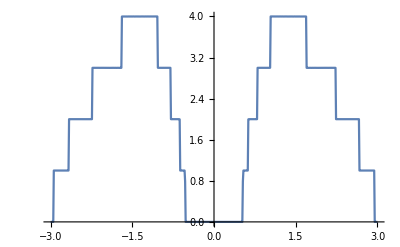

```mathematica
ListPlot[%15,Joined->True]
```

```mathematica
Clear[list,dist]
```

```mathematica
list[num_,m_]:=Transpose[Join[{Range[1,100]},{RandomSample[Join[Table[0,100-num],Table[RandomSample[Join[Range[3,17,1]],1],num]//Flatten]]}]]
```

```mathematica
dist[num_]:=dist[num]=Table[list[num,9],5000]
```

```mathematica
Module[{κ=β[1,0.0001,1,-0.5,0.5,9],n= dist[[1]][[1,2]]},If[n==0,κ,ReplacePart[κ,{{n-1,n},{n,n-1},{n+1,n},{n,n+1}}->0]]]
```

```mathematica
device[ω_,δ_,t_,ϵ_,m_,number_,conc_]:=Module[{},
sl1= Module[{J=SL[ω,δ,t,0,0,m]},Do[J=Inverse[IdentityMatrix[2m]-Inverse[Module[{κ=β[ω,δ,t,0,0,m],n= dist[conc][[number]][[loc1,2]]},If[n==0,κ,ReplacePart[κ,{{n-1,n},{n,n-1},{n+1,n},{n,n+1},{19-n,n},{n,19-n}}->0]]]].Module[{κ=ConjugateTranspose[T1[t,9]],n= dist[conc][[1]][[loc1,2]]},If[n==0,κ,ReplacePart[κ,{{19-n,n}}->0]]].J.Module[{κ=T1[t,9],n= dist[conc][[1]][[loc1,2]]},If[n==0,κ,ReplacePart[κ,{{n,19-n}}->0]]]].Inverse[Module[{κ=β[ω,δ,t,0,0,m],n= dist[conc][[number]][[loc1,2]]},If[n==0,κ,ReplacePart[κ,{{n-1,n},{n,n-1},{n+1,n},{n,n+1},{19-n,n},{n,19-n}}->0]]]],{loc1,100}];
 J=J];
il1:=Inverse[IdentityMatrix[2m]-sl1.ρ[1,m].SR[ω,δ,t,0,0,m].ConjugateTranspose[ρ[1,m]]].sl1;
ir1:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,0,0,m].ρ[1,m].sl1.ρ[1,m]].SR[ω,δ,t,0,0,m];gdd1:=il1-ConjugateTranspose[il1];grr1:= ir1-ConjugateTranspose[ir1];Gnonlocal1:= SR[ω,δ,t,0,0,m].ρ[1,m].il1;GNON1:=Gnonlocal1-ConjugateTranspose[Gnonlocal1];tr1=Abs[Tr[gdd1.ρ[1,m].grr1.ρ[1,m]-ρ[1,m].GNON1.ρ[1,m].GNON1]];tr1]
```

```mathematica
Mean[ParallelTable[device[1.5,0.0001,1,0,9,num,10],{num,200}]]//AbsoluteTiming
```

{4.67469,0.483323}

```mathematica
Table[Mean[ParallelTable[device[1.,0.0001,1,0,9,num,x],{num,200}]],{x,Range[10,80,10]}]
```

{0.616595,0.613295,0.766557,1.14508,1.4077,1.47433,1.5115,1.70932}

```mathematica
Table[Print[x];Export["/home/shardulmukim/PhD/fwi/AGNR/vac/9agnr_"<>ToString[x]<>"_vac.dat",Table[{ω,Mean[ParallelTable[device[ω,0.0001,1,0,9,num,x],{num,2000}]]},{ω,Range[-3,3,0.01]}]],{x,10,90,10}]
```

$Aborted

```mathematica
input= Table[ParallelTable[device[ω,0.0001,1,0,9,num,40],{ω,Range[0,3,0.01]}],{num,4000,4100}]
```

{1}
 |  |  |  |

```mathematica
transmission= Table[Import["/home/shardulmukim/PhD/fwi/AGNR/vac/9agnr_"<>ToString[x]<>"_vac.dat"],{x,10,80,10}]
```

{1}
 |  |  |  |

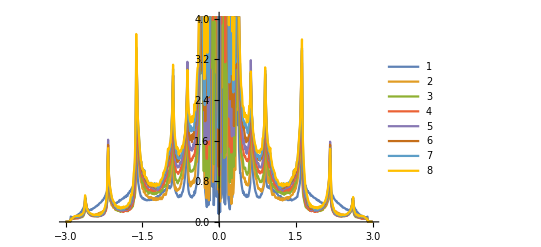

```mathematica
ListLinePlot[transmission,PlotLegends->Automatic]
```

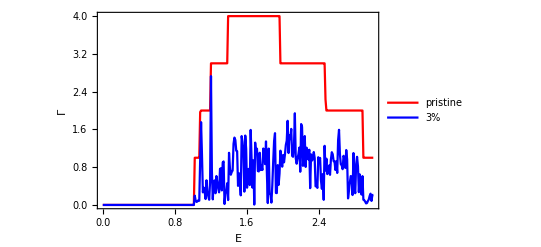

```mathematica
ListLinePlot[{Table[{ω,pris[ω,0.0001,1,1,-0.75,9]},{ω,Range[0,3,0.01]}],Table[{ω,device[ω,0.0001,1,0.5,9,212]},{ω,Range[0,3,0.01]}]},Frame->True,PlotStyle->{Red,Blue},FrameLabel->{{Γ,None},{Ε,None}},PlotLegends->Placed[{"pristine","3%"},{{0.2,0.8}}],LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

```mathematica
Table[Print["working on "<>ToString[a]<>""];Export["/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_"<>ToString[a]<>"_0.5.dat",Table[{ω,Mean[ParallelTable[device[ω,0.0001,1,0.5,9,a,0],500]]},{ω,Range[0,3.5,0.01]}]],{a,Range[10,80,5]}]
```

```mathematica
CA=Table[Import["/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_"<>ToString[x]<>"_vac.dat"],{x,Range[10,70,10]}]
```

{{{-3.,0.000378278},{-2.99,0.000450874},{-2.98,0.000656547},{-2.97,0.000916178},{-2.96,0.00159303},{-2.95,0.0032898},{-2.94,0.139154},{-2.93,0.12427},{-2.92,0.116288},{-2.91,0.120353},{-2.9,0.113196},{-2.89,0.131868},{-2.88,0.115839},{-2.87,0.128208},{-2.86,0.148254},{-2.85,0.141412},{-2.84,0.14897},568,{2.85,0.144851},{2.86,0.139901},{2.87,0.131778},{2.88,0.126764},{2.89,0.122791},{2.9,0.119549},{2.91,0.120562},{2.92,0.113154},{2.93,0.124115},{2.94,0.139179},{2.95,0.00352395},{2.96,0.00150488},{2.97,0.000864057},{2.98,0.000741185},{2.99,0.000477352},{3.,0.000393072}},6}
 |  |  |  |

```mathematica
Dimensions[%48]
```

{7,601,2}

```mathematica
Dimensions[transmission]
```

{9,601,2}

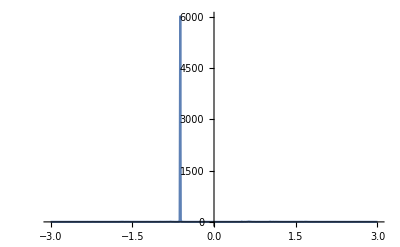

```mathematica
ListLinePlot[Transpose[Join[{Range[-3,3,0.01]},{input[[5]]}]],PlotRange->All]
```

```mathematica
misfit16[n_,x_,y_]:=Module[{m5=Transpose[Join[{Range[0,3,0.01]},{input[[n]]}]]},
ρ1:= Table[Module[{B1=Transpose[{m5[[1;;301]][[;;,1]],(m5[[1;;301,2]]-transmission[[ξ]][[1;;301,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{ξ,9}]; 
a1=Transpose[Join[{Range[10,90,10]},{ρ1}]];{a1,a1[[Position[a1,Min[a1]][[1,1]]]]}]
```

```mathematica
Table[misfit16[n,3,1][[2]],{n,100}]
```

{{60,0.00197484},{80,0.00929644},{50,0.00449372},{20,0.00170431},{30,0.00141193},{30,0.00171607},{70,0.00278587},{60,0.00355957},{30,0.00163852},{30,0.00185381},{30,0.00216395},{60,0.00263047},{30,0.00171703},{20,0.00132365},{30,0.00166875},{80,0.0250997},{60,0.00213816},{90,0.0129032},{70,0.0019848},{30,0.00144235},{40,0.00479935},{40,0.00254351},{20,0.00114894},{30,0.00163638},{30,0.00176924},{30,0.00175313},{30,0.0028213},{30,0.0014265},{10,0.00192722},{50,0.00127848},{70,0.00249088},{50,0.00325006},{90,0.00184563},{40,0.00215326},{20,0.00230242},{60,0.00310743},{30,0.00214522},{40,0.00199182},{50,0.00217566},{30,0.0018093},{30,0.00341926},{30,0.00139936},{70,0.00273821},{90,0.03023},{30,0.00225496},{70,0.00853052},{40,0.00239063},{80,0.0109032},{50,0.00311271},{30,0.00144735},{30,0.00189487},{30,0.00193403},{50,0.00149001},{30,0.00242944},{40,0.00178342},{50,0.00229959},{70,0.00238306},{50,0.00291691},{30,0.00155138},{80,0.00894803},{90,0.00654239},{30,0.00145697},{80,0.0473678},{40,0.00193183},{60,0.00229807},{70,0.00475205},{30,0.00115526},{70,0.00304127},{20,0.0017773},{50,0.00236449},{90,0.0335382},{30,0.00222275},{20,0.00148062},{30,0.00138169},{40,0.0024878},{30,0.00224604},{60,0.00289522},{40,0.00585578},{30,0.00123407},{30,0.00235665},{40,0.00390359},{30,0.00275515},{20,0.00216299},{40,0.00563995},{30,0.00510174},{80,0.00314514},{70,0.00245803},{60,0.00142793},{40,0.00140612},{50,0.00400979},{50,0.00198429},{90,0.00680305},{50,0.00238875},{40,0.00346334},{80,0.00702369},{60,0.00328913},{80,0.00683172},{30,0.00136231},{20,0.00143179},{40,0.00152521}}

```mathematica
dist[40][[2]]
```

{{1,8},{2,4},{3,0},{4,11},{5,0},{6,0},{7,9},{8,0},{9,6},{10,15},{11,0},{12,0},{13,15},{14,0},{15,0},{16,0},{17,12},{18,15},{19,9},{20,9},{21,15},{22,7},{23,0},{24,0},{25,11},{26,8},{27,0},{28,0},{29,0},{30,16},{31,0},{32,0},{33,5},{34,0},{35,0},{36,0},{37,0},{38,13},{39,0},{40,11},{41,0},{42,0},{43,0},{44,0},{45,13},{46,0},{47,9},{48,0},{49,6},{50,17},{51,0},{52,0},{53,3},{54,5},{55,8},{56,0},{57,7},{58,0},{59,12},{60,15},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0},{67,0},{68,15},{69,0},{70,0},{71,0},{72,16},{73,0},{74,0},{75,5},{76,0},{77,0},{78,7},{79,0},{80,0},{81,0},{82,10},{83,0},{84,0},{85,9},{86,0},{87,0},{88,3},{89,7},{90,17},{91,10},{92,0},{93,0},{94,0},{95,0},{96,0},{97,4},{98,0},{99,0},{100,0}}

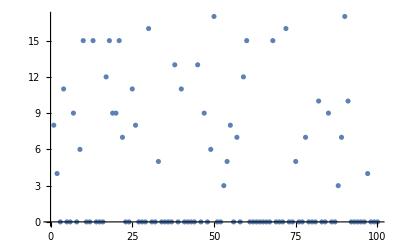

```mathematica
ListPlot[%143]
```

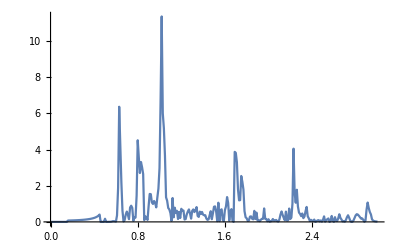

```mathematica
ListLinePlot[Transpose[Join[{Range[0,3,0.01]},{input[[2]]}]],PlotRange->All]
```

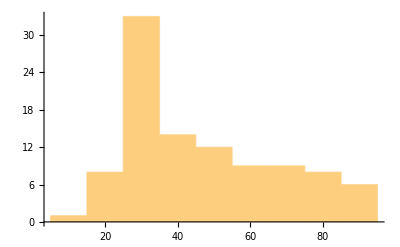

```mathematica
Histogram[Table[misfit16[n,3,1][[2]][[1]],{n,100}]]
```